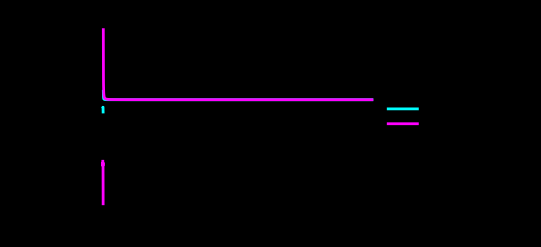

-Graphics3D-

```mathematica
(*Final Audit:Asymptotic Convergence and Observable Decay*)ClearAll["Global`*"];

(*Constants*)
R=1.15428;
tauRelax=20; (*20 Gyr Relaxation Horizon*)

(*Grover Potential Function with Scale Parameter s*)
V[r_,s_]:=(s/(r^2+0.1))+R*Log[r+s];

(*1. Relative Difference (Asymptotic Bound)*)
(*Proving|Vi-Vj| /Vi->0 as r->Infinity*)
RelativeDiff[r_,s1_,s2_]:=Abs[V[r,s1]-V[r,s2]]/V[r,s1];

(*2. Apparent Dark Matter Fraction fDM(r,t)*)
(*Metric Memory decays over time t and distance r*)
fDM[r_,t_]:=(R*Log[r+1])*Exp[-t/tauRelax]/(1/r+0.1);

(*---Visualization 1:The Vanishing Bound---*)
Plot[Evaluate[Table[RelativeDiff[r,0.05,s2],{s2,{1.0,10.0}}]],{r,0.1,500},PlotRange->All,PlotStyle->{Cyan,Magenta},Frame->True,FrameLabel->{"Radius (Log r)","Relative Error (Convergence)"},PlotLegends->{"Quantum vs Galactic","Quantum vs Cosmic"},PlotLabel->"Structural Closure: Asymptotic Convergence Limit",Background->Black,FrameStyle->White]

(*---Visualization 2:The Observable Relaxation---*)
Plot3D[fDM[r,t],{r,1,50},{t,0,40},PlotRange->All,AxesLabel->{"Radius","Time (Gyr)","f_DM"},MeshFunctions->{#3&},ColorFunction->"TemperatureMap",PlotLabel->"Observable: Dark Matter Fraction Decay (r, t)",Boxed->False,Background->Black]
```